```mathematica
Print[Button[Style["Quit Kernel",Bold],Quit[],ImageSize->{150,35}]]
```

Quit Kernel

Folgendes Integral soll minimiert bzw. maximiert (Vorzeichen des Integrandens wird invertiert) werden:

ℐ=∫_t_1^t_2 F(t,𝓏_1, (𝓏̇)_1,𝓏_2)ⅆt→min , bzw.  ℐ=∫_t_1^t_2 -F(t,𝓏_1, (𝓏̇)_1,𝓏_2)ⅆt→max

In dem Funktionenvektor 𝓏_1 sind alle Funktionen enthalten, deren erste Ableitungen in F(t,𝓏_1, (𝓏̇)_1,𝓏_2) vorkommen.
In dem Funktionenvektor 𝓏_2 hingegen sind alle Funktionen enthalten, deren erste Ableitungen in F(t,𝓏_1, (𝓏̇)_1,𝓏_2) nicht vorkommen. 𝓏_2 ist in der Regel ausschließlich im 3. Fall vorhanden!

2. Fall: Ein weiteres Integral soll einen festen Wert τ annehmen:

τ=∫_t_1^t_2 G(t,𝓏_1, (𝓏̇)_1)ⅆt

Für das resultierende Differentialgleichungssystem gilt:

H(t,𝓏_1, (𝓏̇)_1,λ)=F(t,𝓏_1, (𝓏̇)_1)+λ G(t,𝓏_1, (𝓏̇)_1)
0=∇_𝓏_1 H(t,𝓏_1, (𝓏̇)_1,λ)-ⅆ/ⅆt∇_((𝓏̇)_1) H(t,𝓏_1, (𝓏̇)_1,λ)

## Eingabe (F, 𝓏_1, 𝓏_2, 𝓃ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃, G)

```mathematica
ClearAll["Global`*"]
F[x_]=-y[x]^2;
𝓏1[x_]={y[x]};
𝓏2[x_]={};
𝓃ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃={y[0]==0,y[X]==1};
G[x_]=1-2 D[y[x],x]^2;
```

## Programm (automatisch)

```mathematica
(*Programm*)
<<VariationalMethods`
H[x_]=F[x]+λAllgemein G[x];
𝓏[x_]=Join[𝓏1[x],𝓏2[x]];
𝒹ℊℓ𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽=Table[
FullSimplify[VariationalD[H[x],𝓏[x],x]][[i]]==0,
{i,Length[𝓏[x]]}];

(*Ausgabe*)
Print[StringForm["``",
𝒹ℊℓ𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽//TableForm]]
```

-2 y[x]+4 λAllgemein y''[x]==0

## Programm (manuell)

```mathematica
(*Programm*)
H[x_]=F[x]+λAllgemein G[x];
𝓏[x_]=Join[𝓏1[x],𝓏2[x]];
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ=Table[
FullSimplify[(Grad[H[x],𝓏[x]]-D[Grad[H[x],D[𝓏[x],x]],x])][[i]]==0,
{i,Length[𝓏[x]]}];

(*Ausgabe*)
Print[StringForm["``",
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ//TableForm]]
```

-2 y[x]+4 λAllgemein y''[x]==0

0=-2 y[x]+4 λAllgemein y''[x]
0=y[x]-2 λAllgemein y''[x]

```mathematica
(*Programm*)
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ={y[x]-2 λAllgemein y''[x]==0};

(*Ausgabe*)
Print[StringForm["``",
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ//TableForm]]
```

y[x]-2 λAllgemein y''[x]==0

## Programm (Differentialgleichung)

```mathematica
(*Programm*)
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[x_]=Flatten[FullSimplify[N[DSolve[Join[𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ,𝓃ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃],𝓏[x],x]]]][[All,2]];

(*Ausgabe*)
Print[StringForm["𝓎_allgemein(x) = ``",
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[x]//MatrixForm]]
```

𝓎_allgemein(x) = ((ⅇ^((-0.707107 x+0.707107 X)/(√λAllgemein)) (-1.+ⅇ^((1.41421 x)/(√λAllgemein))))/(-1.+ⅇ^((1.41421 X)/(√λAllgemein))))

## Programm (λ)

X beträgt 1. Für y_allgemein(x) gilt dann:

```mathematica
(*Programm*)
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[x_]=(ⅇ^((-0.7071067811865475 x+0.7071067811865475)/(√λAllgemein)) (-1+ⅇ^((1.4142135623730951 x)/(√λAllgemein))))/(-1+ⅇ^(1.4142135623730951/(√λAllgemein)));

(*Ausgabe*)
Print[StringForm["𝓎_allgemein(x) = ``",
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[x]//MatrixForm]]
```

𝓎_allgemein(x) = (ⅇ^((0.707107-0.707107 x)/(√λAllgemein)) (-1+ⅇ^((1.41421 x)/(√λAllgemein))))/(-1+ⅇ^(1.41421/(√λAllgemein)))

```mathematica
Print[FullSimplify[D[(ⅇ^((0.7071067811865475-0.7071067811865475 x)/(√λAllgemein)) (-1+ⅇ^((1.4142135623730951 x)/(√λAllgemein))))/(-1+ⅇ^(1.4142135623730951/(√λAllgemein))),x]^2]]
```

(0.5 ⅇ^((1.41421-1.41421 x)/(√λAllgemein)) (1.+1. ⅇ^((1.41421 x)/(√λAllgemein)))^2)/((-1.+ⅇ^(1.41421/(√λAllgemein)))^2 λAllgemein)

y_allgemein(x)=(0.5 ⅇ^((1.41421-1.41421 x)/(√λAllgemein)) (1.+1. ⅇ^((1.41421 x)/(√λAllgemein)))^2)/((-1.+ⅇ^(1.41421/(√λAllgemein)))^2 λAllgemein)

𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽 entspricht den Integrationsgrenzen bzw. den Nebenbedingungen:

```mathematica
G=1-(ⅇ^((1.414213562373095-1.414213562373095 x)/(√λAllgemein)) (0.9999999999999997+1. ⅇ^((1.414213562373095 x)/(√λAllgemein)))^2)/((-1.+ⅇ^(1.414213562373095/(√λAllgemein)))^2 λAllgemein);
𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽={0,1};
```

```mathematica
$Assumptions=λAllgemein∈Reals;
Print[Chop[Integrate[G,{x,𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[1]],𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[2]]}]]]
```

1+(-2. ⅇ^(1.41421/(√λAllgemein))+0.707107 √λAllgemein-0.707107 ⅇ^(2.82843/(√λAllgemein)) √λAllgemein)/((-1.+ⅇ^(1.41421/(√λAllgemein)))^2 λAllgemein)

Solve[…] funktioniert nicht, daher wird Newton’sches Verfahren (FindRoot[…])  verwendet:

τ=4=1+(-2. ⅇ^(1.41421/(√λAllgemein))+0.707107 √λAllgemein-0.707107 ⅇ^(2.82843/(√λAllgemein)) √λAllgemein)/((-1.+ⅇ^(1.41421/(√λAllgemein)))^2 λAllgemein)
0=-3+(-2. ⅇ^(1.41421/(√λAllgemein))+0.707107 √λAllgemein-0.707107 ⅇ^(2.82843/(√λAllgemein)) √λAllgemein)/((-1.+ⅇ^(1.41421/(√λAllgemein)))^2 λAllgemein)

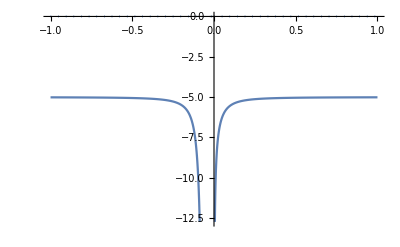

```mathematica
Print[ReImPlot[-3+(-1.9999999999999993 ⅇ^(1.414213562373095/(√λAllgemein))+0.7071067811865471 √λAllgemein-0.7071067811865476 ⅇ^(2.82842712474619/(√λAllgemein)) √λAllgemein)/((-1.+ⅇ^(1.414213562373095/(√λAllgemein)))^2 λAllgemein),{λAllgemein,-1,1},PlotRange->Automatic]]
```

## Plot

𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽 entspricht den Integrationsgrenzen bzw. den Nebenbedingungen:

```mathematica
𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽={0,1};
```

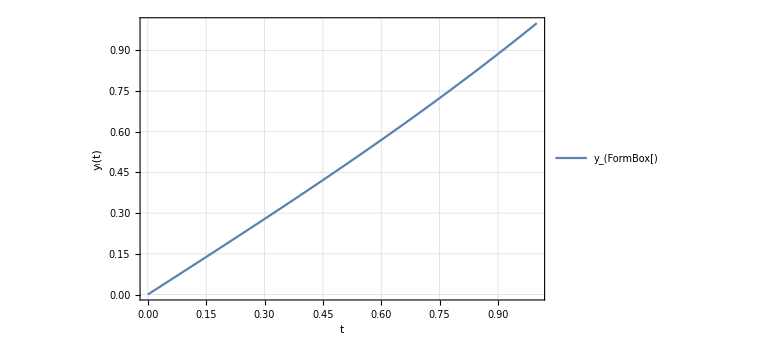

```mathematica
(*Ausgabe*)
plot=Plot[Evaluate[𝓎[t]],{t,𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[1]],𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[2]]},
PlotRange->All,Frame->True,FrameLabel->{"t","y_i(t)"},GridLines->Automatic,
PlotLegends->Table[StringForm["y_(``)",i],{i,Length[𝓎[t]]}],
ImageSize->Large];
Print[Show[plot]]
```